```mathematica
Quit[]
```

# Muon Production in SM - γ-> μ^- μ^+

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
```

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]} -> {F[2,{2}], -F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,1-> 2];
```

```mathematica
topologies1L=CreateTopologies[1,1-> 2,ExcludeTopologies->Reducible];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

Restoring 48 field point(s)

in total: 1 Particles insertion

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 48 field point(s)

in total: 3 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

> Top. 1 ad/bdcd/0.m, 0 diagrams

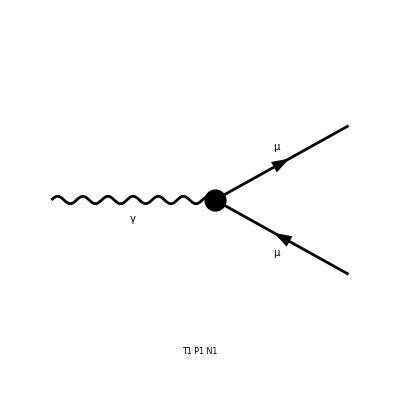

```mathematica
Paint[fieldsBorn];
```

> Top. 1 ad/becf/dedfef.m, 0 diagrams

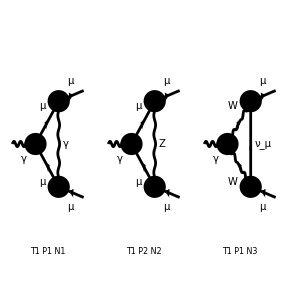

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
myAmpBorn=ExtractAmplitude[ampBorn];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/feynArts_amplitudes/OneLoopAmplitudes.m

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/feynArts_amplitudes/BornAmplitudes.m

## Interference

```mathematica
test=AmpSquare[myAmp1L[[3]],myAmpBorn[[1]]]//Simplify
```

1/(16 π^4)ⅈ EL^4 gAl gWlN gWNl gWWA KiraPropagator[q1,MW] KiraPropagator[-p1+q1,MW] KiraPropagator[-p2+q1,0] ep[V[1],p1,{Lor1}] ep[V[1],p1,{newLor1}] (4 mmsq1 SP[p2,{Lor1}] SP[p2,{newLor1}]-4 mmsq2 SP[p2,{Lor1}] SP[p2,{newLor1}]+8 psq SP[p2,{Lor1}] SP[p2,{newLor1}]-16 SP[p2,q1] SP[p2,{Lor1}] SP[p2,{newLor1}]+8 SP[p2,{Lor1}] SP[p2,{newLor1}] SP[q1,q1]+10 mmsq1 SP[p2,{newLor1}] SP[q1,{Lor1}]-4 d mmsq1 SP[p2,{newLor1}] SP[q1,{Lor1}]+2 mmsq2 SP[p2,{newLor1}] SP[q1,{Lor1}]+12 MLE[2]^2 SP[p2,{newLor1}] SP[q1,{Lor1}]-4 d MLE[2]^2 SP[p2,{newLor1}] SP[q1,{Lor1}]+8 SP[p1,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]-4 d SP[p1,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]-16 SP[p2,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]+8 d SP[p2,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]-2 SP[p1,{newLor1}] (SP[p2,{Lor1}] (3 mmsq1-2 mmsq2+2 psq-MLE[2]^2-4 SP[p1,q1]-4 SP[p2,q1]+2 SP[q1,q1])+(5 mmsq1-2 d mmsq1+MLE[2]^2+2 (-2+d) SP[p2,q1]) SP[q1,{Lor1}])+2 mmsq1 SP[p2,{Lor1}] SP[q1,{newLor1}]+2 mmsq2 SP[p2,{Lor1}] SP[q1,{newLor1}]-8 psq SP[p2,{Lor1}] SP[q1,{newLor1}]-4 MLE[2]^2 SP[p2,{Lor1}] SP[q1,{newLor1}]+4 mmsq1 SP[q1,{Lor1}] SP[q1,{newLor1}]-2 d mmsq1 SP[q1,{Lor1}] SP[q1,{newLor1}]+4 mmsq2 SP[q1,{Lor1}] SP[q1,{newLor1}]-2 d mmsq2 SP[q1,{Lor1}] SP[q1,{newLor1}]-4 psq SP[q1,{Lor1}] SP[q1,{newLor1}]+2 d psq SP[q1,{Lor1}] SP[q1,{newLor1}]-8 MLE[2]^2 SP[q1,{Lor1}] SP[q1,{newLor1}]+4 d MLE[2]^2 SP[q1,{Lor1}] SP[q1,{newLor1}]+SP[p1,{Lor1}] (-2 (-6+d) SP[p1,{newLor1}] (mmsq1-SP[p2,q1])+2 SP[p2,{newLor1}] (-5 mmsq1+d mmsq1+2 mmsq2-2 psq-3 MLE[2]^2+d MLE[2]^2+(-2+d) SP[p1,q1]-2 (-4+d) SP[p2,q1]-2 SP[q1,q1])+(d (mmsq1+mmsq2-psq-2 MLE[2]^2)+6 (-mmsq2+psq+MLE[2]^2)) SP[q1,{newLor1}])+mmsq1^2 SP[{Lor1},{newLor1}]-3 mmsq1 mmsq2 SP[{Lor1},{newLor1}]+2 mmsq2^2 SP[{Lor1},{newLor1}]-3 mmsq1 psq SP[{Lor1},{newLor1}]-4 mmsq2 psq SP[{Lor1},{newLor1}]+2 psq^2 SP[{Lor1},{newLor1}]+mmsq1 MLE[2]^2 SP[{Lor1},{newLor1}]-mmsq2 MLE[2]^2 SP[{Lor1},{newLor1}]+psq MLE[2]^2 SP[{Lor1},{newLor1}]-2 mmsq1 SP[p1,q1] SP[{Lor1},{newLor1}]+4 mmsq2 SP[p1,q1] SP[{Lor1},{newLor1}]-4 psq SP[p1,q1] SP[{Lor1},{newLor1}]-2 MLE[2]^2 SP[p1,q1] SP[{Lor1},{newLor1}]+2 mmsq1 SP[p2,q1] SP[{Lor1},{newLor1}]+2 mmsq2 SP[p2,q1] SP[{Lor1},{newLor1}]+4 psq SP[p2,q1] SP[{Lor1},{newLor1}]-4 MLE[2]^2 SP[p2,q1] SP[{Lor1},{newLor1}]-2 mmsq1 SP[q1,q1] SP[{Lor1},{newLor1}]-2 mmsq2 SP[q1,q1] SP[{Lor1},{newLor1}]+2 psq SP[q1,q1] SP[{Lor1},{newLor1}]+4 MLE[2]^2 SP[q1,q1] SP[{Lor1},{newLor1}])

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_3_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m.

```mathematica
ExtractFamily[test]
```

{{gamma,{MW}}}

```mathematica
ShiftToIntegralFamily[test]
```

{{q1→q1}}

```mathematica
Do[
ShiftAndSave[i,j,False],
{i,3},{j,1}]
```

Integral family {{gamma, {MLE[2]}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_1_1.m.

Integral family {{zeta, {MLE[2], MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_2_1.m.

Integral family {{gamma, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_3_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,3},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_3_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[gamma,{MLE[2]},1,1,1],userIntegral[gamma,{MLE[2]},0,1,1],userIntegral[gamma,{MLE[2]},1,1,0],userIntegral[gamma,{MLE[2]},1,0,1],userIntegral[zeta,{MLE[2],MZ},1,1,1],userIntegral[zeta,{MLE[2],MZ},0,1,1],userIntegral[zeta,{MLE[2],MZ},1,1,0],userIntegral[zeta,{MLE[2],MZ},1,0,1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},0,1,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},1,0,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_myintegrals.m\""}]\).

```mathematica
PrintRules[]
```

{}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[gamma,{MLE[2]},1,1,1],userIntegral[gamma,{MLE[2]},0,1,1],userIntegral[gamma,{MLE[2]},1,1,0],userIntegral[gamma,{MLE[2]},1,0,1],userIntegral[zeta,{MLE[2],MZ},1,1,1],userIntegral[zeta,{MLE[2],MZ},0,1,1],userIntegral[zeta,{MLE[2],MZ},1,1,0],userIntegral[zeta,{MLE[2],MZ},1,0,1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},0,1,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},1,0,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"RESULTS/Coefficients_"<>ToString[i]<>"_1.m")],{i,17}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gFFAZ)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅈ (-1+d) EL^2 gWWAZ)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0},{-(ⅈ EL^2 gFFA gFFZ psq)/(8 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFFA gFFZ (pasq-pzsq)^2)/(64 pasq π^4)},{(ⅈ EL^2 ggmgmA ggmgmZ psq)/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggmgmA ggmgmZ pzsq)/(64 π^4)},{(ⅈ EL^2 ggpgpA ggpgpZ psq)/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggpgpA ggpgpZ pzsq)/(64 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gFAW gFZW SW)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gFAW gFZW SW)/(16 π^4)},{-(ⅈ (-3+2 d) EL^2 gWWA gWWZ psq)/(16 pasq π^4)+(ⅈ EL^2 gWWA gWWZ ((-5+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4)-(ⅈ EL^2 gWWA gWWZ ((-1+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gWWA gWWZ (8 MW^2 pasq+(-7+d) pasq^2-2 (-4+d) pasq pzsq+(-3+d) pzsq^2))/(64 pasq π^4)}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{-(ⅈ EL^2 gFFAZ)/(16 π^4)+(ⅈ (-1+d) EL^2 gWWAZ)/(8 π^4)-(ⅈ EL^2 gFFA gFFZ psq)/(8 pasq π^4)+(ⅈ EL^2 ggmgmA ggmgmZ psq)/(32 pasq π^4)+(ⅈ EL^2 ggpgpA ggpgpZ psq)/(32 pasq π^4)-(ⅈ (-3+2 d) EL^2 gWWA gWWZ psq)/(16 pasq π^4)+(ⅈ EL^2 gWWA gWWZ ((-5+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4)-(ⅈ EL^2 gWWA gWWZ ((-1+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gFFA gFFZ (pasq-pzsq)^2)/(64 pasq π^4)-(ⅈ EL^2 ggmgmA ggmgmZ pzsq)/(64 π^4)-(ⅈ EL^2 ggpgpA ggpgpZ pzsq)/(64 π^4)-(ⅈ EL^2 gWWA gWWZ (8 MW^2 pasq+(-7+d) pasq^2-2 (-4+d) pasq pzsq+(-3+d) pzsq^2))/(64 pasq π^4)+(ⅈ EL^2 gFAW gFZW SW)/(8 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
```

```mathematica
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
coefficients/.parameterReplace/.{pasq->psq,pzsq->psq}//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 MW^2 (CW^2+SW^2))/(8 CW π^4 SW)}

```mathematica
coefficients/.{pasq->psq,pzsq->psq}//Simplify
```

{-1/(32 π^4)ⅈ EL^2 (2 gFFAZ+4 gFFA gFFZ-ggmgmA ggmgmZ-ggpgpA ggpgpZ+4 gWWAZ-4 d gWWAZ-2 gWWA gWWZ+4 d gWWA gWWZ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 (gWWA gWWZ (8 MW^2-2 psq)+ggmgmA ggmgmZ psq+ggpgpA ggpgpZ psq-8 gFAW gFZW SW))/(64 π^4)}

```mathematica
%/.parameterReplace//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 MW^2 (CW^2+SW^2))/(8 CW π^4 SW)}